```mathematica
Build[SetP[7],setp7]
```

Build[SetP[7],setp7]

```mathematica
mat7=Mu[setp7];MatrixPlot[mat7]
```

MatrixPlot::mat0: Argument Mu[setp7] at position 1 is not a matrix.

MatrixPlot[Mu[setp7]]

```mathematica
mat7Inv=Inverse[mat7];
```

```mathematica
Inverse[mat7]//MatrixPlot
```

MatrixPlot::mat0: Argument Inverse[Mu[setp7]] at position 1 is not a matrix.

MatrixPlot[Inverse[Mu[setp7]]]

```mathematica
mat7Inv//Eigenvectors//MatrixRank
```

MatrixRank[Eigenvectors[Inverse[Mu[setp7]]]]

```mathematica
Table[StirlingS2[n,k],{n,10},{k,n}]//TableForm
```

1 |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  | 
1 | 3 | 1 |  |  |  |  |  |  | 
1 | 7 | 6 | 1 |  |  |  |  |  | 
1 | 15 | 25 | 10 | 1 |  |  |  |  | 
1 | 31 | 90 | 65 | 15 | 1 |  |  |  | 
1 | 63 | 301 | 350 | 140 | 21 | 1 |  |  | 
1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1 |  | 
1 | 255 | 3025 | 7770 | 6951 | 2646 | 462 | 36 | 1 | 
1 | 511 | 9330 | 34105 | 42525 | 22827 | 5880 | 750 | 45 | 1

```mathematica
Build[SetP[6],setp6]
```

Build[SetP[6],setp6]

```mathematica
mat6=Mu[setp6];7
```

7

```mathematica
mat6Inv=Inverse[mat6];
```

```mathematica
mat6Inv//Eigenvectors//MatrixRank
```

MatrixRank[Eigenvectors[Inverse[Mu[setp6]]]]

```mathematica
Build[SetP[8],setp8]
```

Build[SetP[8],setp8]

```mathematica
mat8=Mu[setp8];
```

```mathematica
mat8Inv=ZetaP[setp8];
```

```mathematica
MatrixPlot[mat8Inv]
```

MatrixPlot::mat0: Argument ZetaP[setp8] at position 1 is not a matrix.

MatrixPlot[ZetaP[setp8]]

```mathematica
vec=mat8Inv//Eigenvectors;
```

```mathematica
MatrixRank[vec]
```

MatrixRank[Eigenvectors[ZetaP[setp8]]]

```mathematica
vec//DeleteDuplicates//Length
```

1

```mathematica
vec//DeleteDuplicates//MatrixRank
```

MatrixRank[Eigenvectors[ZetaP[setp8]]]

```mathematica
Build[SetP[3],setp3]
```

Build[SetP[3],setp3]

```mathematica
mat3Inv=ZetaP[setp3];
```

```mathematica
Eigenvectors[mat3Inv]//MatrixForm
```

Eigenvectors[ZetaP[setp3]]

```mathematica
Table[allGraphs3[k,"graph"],{k,allGraphs3AtomKeys }]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixForm[ConversionMatrix3["E","C"]]
```

(1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1)

```mathematica
RepGraph3["C"]
```

{v1x2x3→-Graphics-13,v12x3→-Graphics-22,v13x2→-Graphics-16,v1x23→-Graphics-14,v123→-Graphics-26}

```mathematica
Table[allGraphs3[k,"graph"]->(allGraphs3[k,"colofour"]/.RepGraph3["C"]),{k,allGraphs3NullAtomKeys}]//TableForm
```

-Graphics-→-Graphics-26+-Graphics-22+-Graphics-16+-Graphics-14+-Graphics-13
-Graphics-→-Graphics-26+-Graphics-22
-Graphics-→-Graphics-26
-Graphics-→-Graphics-26+-Graphics-16
-Graphics-→-Graphics-26+-Graphics-14

```mathematica
mat1=Table[Table[k,{i,5}],{k,Map[First,RepGraph3["C"]]}]
```

{{v1x2x3,v1x2x3,v1x2x3,v1x2x3,v1x2x3},{v12x3,v12x3,v12x3,v12x3,v12x3},{v13x2,v13x2,v13x2,v13x2,v13x2},{v1x23,v1x23,v1x23,v1x23,v1x23},{v123,v123,v123,v123,v123}}

```mathematica
mat1//MatrixForm
```

(v1x2x3 | v1x2x3 | v1x2x3 | v1x2x3 | v1x2x3
v12x3 | v12x3 | v12x3 | v12x3 | v12x3
v13x2 | v13x2 | v13x2 | v13x2 | v13x2
v1x23 | v1x23 | v1x23 | v1x23 | v1x23
v123 | v123 | v123 | v123 | v123)

```mathematica
mat2=ConversionMatrix3["E","C"];
```

```mathematica
mat2//MatrixForm
```

(1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1)

```mathematica
Table[If[mat2[[j,i]]==1,mat1[[j,i]],0],{i,5},{j,5}]/.RepGraph3["C"]//MatrixForm
```

(-Graphics-13 | 0 | 0 | 0 | 0
-Graphics-13 | -Graphics-22 | 0 | 0 | 0
-Graphics-13 | 0 | -Graphics-16 | 0 | 0
-Graphics-13 | 0 | 0 | -Graphics-14 | 0
-Graphics-13 | -Graphics-22 | -Graphics-16 | -Graphics-14 | -Graphics-26)

```mathematica
MatrixForm[ConversionMatrix3["E","C"].Table[Table[k,{i,5}],{k,Map[First,RepGraph3["C"]]}]]
```

(v123+v12x3+v13x2+v1x23+v1x2x3 | v123+v12x3+v13x2+v1x23+v1x2x3 | v123+v12x3+v13x2+v1x23+v1x2x3 | v123+v12x3+v13x2+v1x23+v1x2x3 | v123+v12x3+v13x2+v1x23+v1x2x3
v123+v12x3 | v123+v12x3 | v123+v12x3 | v123+v12x3 | v123+v12x3
v123+v13x2 | v123+v13x2 | v123+v13x2 | v123+v13x2 | v123+v13x2
v123+v1x23 | v123+v1x23 | v123+v1x23 | v123+v1x23 | v123+v1x23
v123 | v123 | v123 | v123 | v123)

```mathematica
mat3=Eigenvectors[mat2]//Transpose
```

{{0,0,1,0,0},{-1,-1,0,0,0},{0,1,0,0,0},{1,0,0,0,0},{0,0,0,0,0}}

```mathematica
Eigenvalues[mat2]
```

{1,1,1,1,1}

```mathematica
mat3//MatrixForm
```

(0 | 0 | 1 | 0 | 0
-1 | -1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
Table[Table[mat3[[r,c]]*mat1[[r,c]],{r,5} ],{c,5}]/.RepGraph3["C"]//MatrixForm
```

(0 | --Graphics-22 | 0 | -Graphics-14 | 0
0 | --Graphics-22 | -Graphics-16 | 0 | 0
-Graphics-13 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

## Now for four

```mathematica
mat1=Table[Table[k,{i,15}],{k,Map[First,RepGraph4["C"]]}]
```

{{v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4,v1x2x3x4},{v12x3x4,v12x3x4,v12x3x4,v12x3x4,v12x3x4,v12x3x4,v12x3x4,v12x3x4,v12x3x4,v12x3x4,v12x3x4,v12x3x4,v12x3x4,v12x3x4,v12x3x4},{v13x2x4,v13x2x4,v13x2x4,v13x2x4,v13x2x4,v13x2x4,v13x2x4,v13x2x4,v13x2x4,v13x2x4,v13x2x4,v13x2x4,v13x2x4,v13x2x4,v13x2x4},{v14x2x3,v14x2x3,v14x2x3,v14x2x3,v14x2x3,v14x2x3,v14x2x3,v14x2x3,v14x2x3,v14x2x3,v14x2x3,v14x2x3,v14x2x3,v14x2x3,v14x2x3},{v1x23x4,v1x23x4,v1x23x4,v1x23x4,v1x23x4,v1x23x4,v1x23x4,v1x23x4,v1x23x4,v1x23x4,v1x23x4,v1x23x4,v1x23x4,v1x23x4,v1x23x4},{v1x24x3,v1x24x3,v1x24x3,v1x24x3,v1x24x3,v1x24x3,v1x24x3,v1x24x3,v1x24x3,v1x24x3,v1x24x3,v1x24x3,v1x24x3,v1x24x3,v1x24x3},{v1x2x34,v1x2x34,v1x2x34,v1x2x34,v1x2x34,v1x2x34,v1x2x34,v1x2x34,v1x2x34,v1x2x34,v1x2x34,v1x2x34,v1x2x34,v1x2x34,v1x2x34},{v123x4,v123x4,v123x4,v123x4,v123x4,v123x4,v123x4,v123x4,v123x4,v123x4,v123x4,v123x4,v123x4,v123x4,v123x4},{v124x3,v124x3,v124x3,v124x3,v124x3,v124x3,v124x3,v124x3,v124x3,v124x3,v124x3,v124x3,v124x3,v124x3,v124x3},{v12x34,v12x34,v12x34,v12x34,v12x34,v12x34,v12x34,v12x34,v12x34,v12x34,v12x34,v12x34,v12x34,v12x34,v12x34},{v134x2,v134x2,v134x2,v134x2,v134x2,v134x2,v134x2,v134x2,v134x2,v134x2,v134x2,v134x2,v134x2,v134x2,v134x2},{v13x24,v13x24,v13x24,v13x24,v13x24,v13x24,v13x24,v13x24,v13x24,v13x24,v13x24,v13x24,v13x24,v13x24,v13x24},{v14x23,v14x23,v14x23,v14x23,v14x23,v14x23,v14x23,v14x23,v14x23,v14x23,v14x23,v14x23,v14x23,v14x23,v14x23},{v1x234,v1x234,v1x234,v1x234,v1x234,v1x234,v1x234,v1x234,v1x234,v1x234,v1x234,v1x234,v1x234,v1x234,v1x234},{v1234,v1234,v1234,v1234,v1234,v1234,v1234,v1234,v1234,v1234,v1234,v1234,v1234,v1234,v1234}}

```mathematica
mat1b=mat1/.RepGraph4["C"]
```

{{-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364,-Graphics-364},{-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607,-Graphics-607},{-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445,-Graphics-445},{-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391,-Graphics-391},{-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373,-Graphics-373},{-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367,-Graphics-367},{-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365,-Graphics-365},{-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697,-Graphics-697},{-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637,-Graphics-637},{-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608,-Graphics-608},{-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473,-Graphics-473},{-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448,-Graphics-448},{-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400,-Graphics-400},{-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377,-Graphics-377},{-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728,-Graphics-728}}

```mathematica
mat2=ConversionMatrix4["E","C"];
```

```mathematica
mat3=Eigenvectors[mat2]//Sort
```

{{0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,-1,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,1,1,-2,1,-2,-2,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

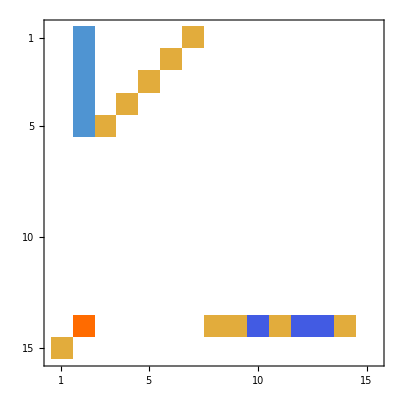

```mathematica
MatrixPlot[mat3]
```

```mathematica
MatrixForm[mat3]
```

(0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -2 | 1 | -2 | -2 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
DeleteDuplicates[mat3]
```

{{0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,-1,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,1,1,-2,1,-2,-2,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
mat3[[2,1]]
```

0

```mathematica
Table[Table[mat3[[r,c]]*mat1b[[c,r]],{r,1,15} ],{c,1,15}]//Transpose//MatrixForm
```

(0 | --Graphics-607 | 0 | 0 | 0 | 0 | -Graphics-365 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | --Graphics-607 | 0 | 0 | 0 | -Graphics-367 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | --Graphics-607 | 0 | 0 | -Graphics-373 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | --Graphics-607 | 0 | -Graphics-391 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | --Graphics-607 | -Graphics-445 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 -Graphics-607 | 0 | 0 | 0 | 0 | 0 | -Graphics-697 | -Graphics-637 | -2 -Graphics-608 | -Graphics-473 | -2 -Graphics-448 | -2 -Graphics-400 | -Graphics-377 | 0
-Graphics-364 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)